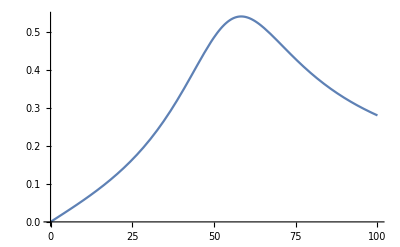

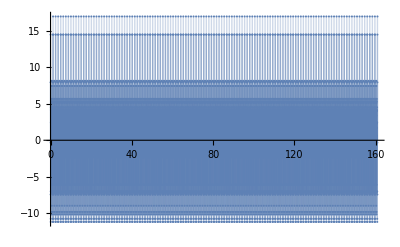

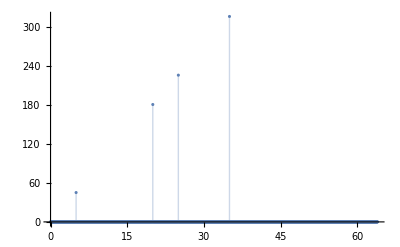

0.26944026361

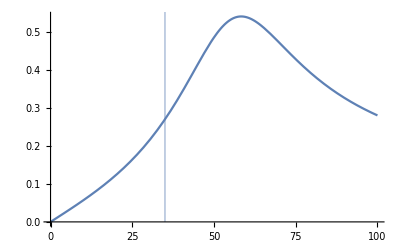

```mathematica
L1=SetPrecision[13.8219802424283,15];
L2=SetPrecision[0.785851503153887,15];
C1=SetPrecision[0.0000114177812859863,15];
C2=SetPrecision[0.0000109238816834688,13];
R1=SetPrecision[101.283800461081,15];
R2=SetPrecision[36.6562072877979,15];
R3=SetPrecision[1048.19925112845,14];
R4=SetPrecision[504.440279684298,15];
dt=SetPrecision[0.0196349540849362,15];
Nel=8192;
t=dt*Nel;


Z1[w_]=R4+1/(I w C2); 
Z2[w_]=1/(I w C1)+R2+I w L2+R3; 
Zparalel[w_]=1/(1/Z1[w]+1/Z2[w]); 
I1[w_]=Uin/(R1+I w L1+Zparalel[w]);
Upar[w_]=I1[w]*Zparalel[w];
Ipar1[w_]=Upar[w]/Z1[w];
Uout[w_]=Ipar1[w]*R4;
H[w_]=Uout[w]/Uin;
Plot[Abs@H[w],{w,0,100}]

signal=ReadList["D:\\Точька\\СПбГЭТУ\\Физика\\10.txt"];
ForPlot=Table[{(i-1)*dt,signal[[i]]},{i,1,Nel}];
ListPlot[ForPlot,Filling->Axis,PlotRange->Full]

Fsig=Fourier[signal];
outN=Length@Fsig;
df=1/t;
FourAbs=Table[{2 π df (i-1),Abs@Fsig[[i]]},{i,1,outN/5}];
ListPlot[FourAbs,Filling->Axis,PlotRange->Full]

Abs@H[35]
Show[Plot[Abs@H[w],{w,0,100}],ListPlot[{{35,3}},Filling->Axis]]
```